# Unit Impulse Train

```mathematica
DiracDelta[t]//TraditionalForm
```

t

```mathematica
Piecewise[{{1,t==0}},0]
```

Piecewise[{{1, t==0}, {0, True}}]

```mathematica
∑_(k=-5)^5 DiracDelta[t-k];
```

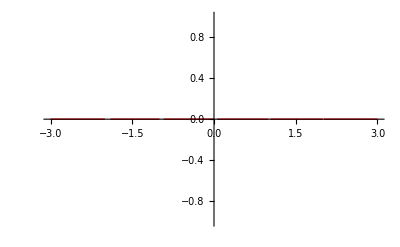

```mathematica
Plot[∑_(k=-5)^5 DiracDelta[t-k],{t,-3,3},PlotStyle->{Red,Thick}]
```

```mathematica
DiscretePlot[∑_(k=-5)^5 DiracDelta[n-k],{n,-3,3,1},PlotMarkers->{"Point",Large},PlotStyle->Red]
```

-Graphics-